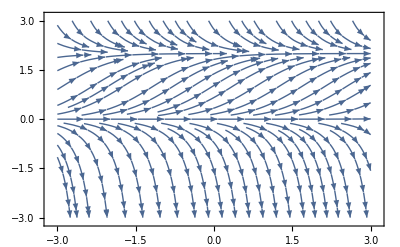

{{x[t]→(2 ⅇ^(2 t))/(ⅇ^(2 t)+ⅇ^(2 C[1]))}}

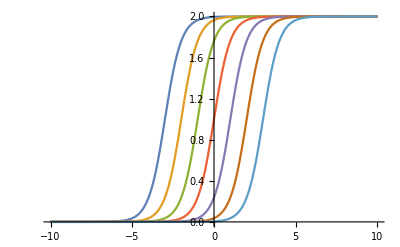

```mathematica
StreamPlot[{1,2x(1-x/2)},{t,-3,3},{x,-3,3},Frame->True,Axes->True,AspectRatio->1/GoldenRatio]
sol = DSolve[x'[t]==2x[t](1-x[t]/2), x[t], t]
Plot[Evaluate[x[t]/.sol/.{C[1]->Range[-3,3]}],{t,-10,10}]
```

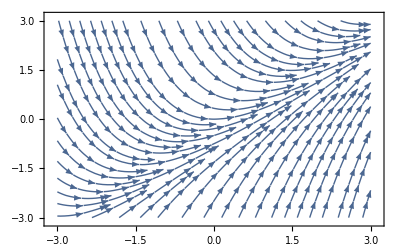

{{x[t]→-1+t+ⅇ^-t C[1]}}

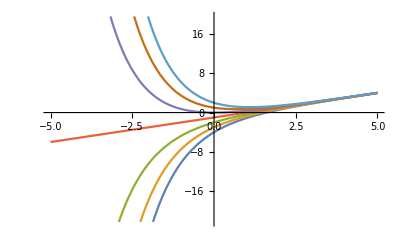

```mathematica
StreamPlot[{1,t-x},{t,-3,3},{x,-3,3},Frame->True,Axes->True,AspectRatio->1/GoldenRatio]
sol = DSolve[x'[t]==t-x[t], x[t], t]
Plot[Evaluate[x[t]/.sol/.{C[1]->Range[-3,3]}],{t,-5,5}]
```

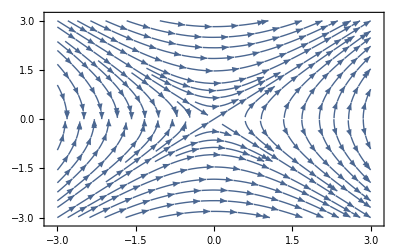

{{x[t]→-√(t^2+2 C[1])},{x[t]→√(t^2+2 C[1])}}

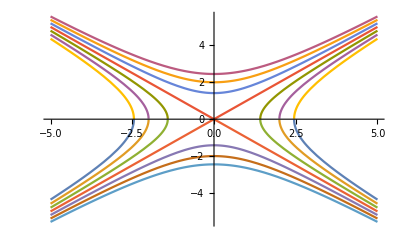

```mathematica
StreamPlot[{1,t/x},{t,-3,3},{x,-3,3},Frame->True,Axes->True,AspectRatio->1/GoldenRatio]
sol = DSolve[x'[t]==t/x[t], x[t], t]
Plot[Evaluate[x[t]/.sol/.{C[1]->Range[-3,3]}],{t,-5,5}]
```